## OLD STUFF: Unitary matrix construction

```mathematica
(*Define the rotation matrix*)
R[i_,j_,n_,θ_]:=Module[{mat=IdentityMatrix[n]},
mat[[i,i]]=Cos[θ];
mat[[i,j]]=-Sin[θ];
mat[[j,i]]=Sin[θ];
mat[[j,j]]=Cos[θ];
mat]

(*Define the phase matrix*)
PhaseMatrix[k_,n_,ϕ_]:=Module[{mat},
mat=IdentityMatrix[n];
mat[[k,k]]=ⅇ^(ⅈ ϕ);
mat]

(*Number of dimensions*)
n=4;

(*Construct the unitary matrix*)
UnitaryMatrix[thetaList_,phiList_]:=Module[{mat},
mat=IdentityMatrix[n];
(*Apply rotations*)
mat=mat.R[1,2,n,thetaList[[1]]];
mat=mat.R[1,3,n,thetaList[[2]]];
mat=mat.R[1,4,n,thetaList[[3]]];
mat=mat.R[2,3,n,thetaList[[4]]];
mat=mat.R[2,4,n,thetaList[[5]]];
mat=mat.R[3,4,n,thetaList[[6]]];
(*Apply phase shifts*)
For[k=1,k<=n,k++,
mat=mat.PhaseMatrix[k,n,phiList[[k]]]];
mat
]

(*Example usage*)
thetaList=Array[Symbol["θ"<>ToString[#]]&,6];
phiList=Array[Symbol["φ"<>ToString[#]]&,4];
FullSimplify[(Transpose[UnitaryMatrix[thetaList,phiList]]/.ⅈ->-ⅈ).UnitaryMatrix[thetaList,phiList]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
UnitaryMatrix[thetaList,phiList]//MatrixForm
```

(ⅇ^(ⅈ φ1) Cos[θ1] Cos[θ2] Cos[θ3] | ⅇ^(ⅈ φ2) (Cos[θ5] (-Cos[θ4] Sin[θ1]-Cos[θ1] Sin[θ2] Sin[θ4])-Cos[θ1] Cos[θ2] Sin[θ3] Sin[θ5]) | ⅇ^(ⅈ φ3) (Cos[θ6] (-Cos[θ1] Cos[θ4] Sin[θ2]+Sin[θ1] Sin[θ4])+(-Cos[θ1] Cos[θ2] Cos[θ5] Sin[θ3]-(-Cos[θ4] Sin[θ1]-Cos[θ1] Sin[θ2] Sin[θ4]) Sin[θ5]) Sin[θ6]) | ⅇ^(ⅈ φ4) (Cos[θ6] (-Cos[θ1] Cos[θ2] Cos[θ5] Sin[θ3]-(-Cos[θ4] Sin[θ1]-Cos[θ1] Sin[θ2] Sin[θ4]) Sin[θ5])-(-Cos[θ1] Cos[θ4] Sin[θ2]+Sin[θ1] Sin[θ4]) Sin[θ6])
ⅇ^(ⅈ φ1) Cos[θ2] Cos[θ3] Sin[θ1] | ⅇ^(ⅈ φ2) (Cos[θ5] (Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ2] Sin[θ4])-Cos[θ2] Sin[θ1] Sin[θ3] Sin[θ5]) | ⅇ^(ⅈ φ3) (Cos[θ6] (-Cos[θ4] Sin[θ1] Sin[θ2]-Cos[θ1] Sin[θ4])+(-Cos[θ2] Cos[θ5] Sin[θ1] Sin[θ3]-(Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ2] Sin[θ4]) Sin[θ5]) Sin[θ6]) | ⅇ^(ⅈ φ4) (Cos[θ6] (-Cos[θ2] Cos[θ5] Sin[θ1] Sin[θ3]-(Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ2] Sin[θ4]) Sin[θ5])-(-Cos[θ4] Sin[θ1] Sin[θ2]-Cos[θ1] Sin[θ4]) Sin[θ6])
ⅇ^(ⅈ φ1) Cos[θ3] Sin[θ2] | ⅇ^(ⅈ φ2) (Cos[θ2] Cos[θ5] Sin[θ4]-Sin[θ2] Sin[θ3] Sin[θ5]) | ⅇ^(ⅈ φ3) (Cos[θ2] Cos[θ4] Cos[θ6]+(-Cos[θ5] Sin[θ2] Sin[θ3]-Cos[θ2] Sin[θ4] Sin[θ5]) Sin[θ6]) | ⅇ^(ⅈ φ4) (Cos[θ6] (-Cos[θ5] Sin[θ2] Sin[θ3]-Cos[θ2] Sin[θ4] Sin[θ5])-Cos[θ2] Cos[θ4] Sin[θ6])
ⅇ^(ⅈ φ1) Sin[θ3] | ⅇ^(ⅈ φ2) Cos[θ3] Sin[θ5] | ⅇ^(ⅈ φ3) Cos[θ3] Cos[θ5] Sin[θ6] | ⅇ^(ⅈ φ4) Cos[θ3] Cos[θ5] Cos[θ6])

```mathematica
UnitaryMatrix[thetaList,phiList]//UnitaryMatrixQ
```

False

## Optimization

```mathematica
⟨v1_,v2_⟩:=Total[v1* v2]
Subscript[σ, i_]:=PauliMatrix[i]
a_⊙b_:=KroneckerProduct[a,b]
c[n_]:=If[n==0,1,n+1]
n_:=UnitVector[2,c[n]]
n_:=Transpose[UnitVector[2,c[n]]] (*not used*)
a_,b_:=Flatten[a⊙b]
(*ρ is the list of the 4 terms {0000,0010,1000,1010}*)
ρ={0,0⊙0,0,0,0⊙1,0,1,0⊙0,0,1,0⊙1,0};
(*P is the list of the 4 terms {00,01,10,11}*)
P={0⊙0,0⊙1,1⊙0,1⊙1};

K[p_]:={√p Subscript[σ, 0],√(1-p)Subscript[σ, 3]};
(*Construction of U(4) from [PHYSICAL REVIEW A 69,010301~R!~2004!]*)
(*SU(2) in eq. 6 from https://www.tamagawa.jp/research/quantum/bulletin/pdf/Tamagawa.Vol.5-5.pdf*)
U2[α_,β_,γ_]:=({{ⅇ^(-ⅈ (γ+α)/2)Cos[β/2], -ⅇ^(ⅈ (γ-α)/2)Sin[β/2]}, {ⅇ^(-ⅈ (γ-α)/2)Sin[β/2], ⅇ^(ⅈ (γ+α)/2)Cos[β/2]}})
cnot=(0⊙0)⊙Subscript[σ, 0]+(1⊙1)⊙Subscript[σ, 1];
u2[h_]:=-u3(Cos[h-π/4] Subscript[σ, 0]-ⅈ Subscript[σ, 1] Sin[h-π/4])
v2[h_]:=Cos[h] Subscript[σ, 0]-ⅈ Subscript[σ, 3] Sin[h]
u3=-ⅈ/(√2)(Subscript[σ, 1]+Subscript[σ, 3]);
w=(Subscript[σ, 0]-ⅈ Subscript[σ, 1])/(√2);
U=((U2[α3,β3,γ3].w)⊙(U2[α4,β4,γ4].Inverse[w])).cnot.(u3⊙(v2[hy])*).cnot.(u2[hx]⊙v2[hz]).cnot.(U2[α1,β1,γ1]⊙U2[α2,β2,γ2]);
ϕ=1/(√2){1,0,0,1};
(*partial traces on the first and the second part of matrices*)
Γb:=Tr[Partition[#,{4,4}],Plus,2]&
pt:=Map[Tr,Partition[#,{2,2}],{2}]&
(*projection*)
pr=IdentityMatrix[4]⊙({{1, 0}, {0, 0}});
ρout[p_]:=pt[pr.(∑_(m=1)^4 (P[[m]]⊙(U†.(∑_(i=1)^2 ∑_(j=1)^2 (K[p][[i]]⊙K[p][[j]]).U.ρ[[m]].U†.(K[p][[i]]⊙K[p][[j]])†).U))).pr]/Tr[pt[pr.(∑_(m=1)^4 (P[[m]]⊙(U†.(∑_(i=1)^2 ∑_(j=1)^2 (K[p][[i]]⊙K[p][[j]]).U.ρ[[m]].U†.(K[p][[i]]⊙K[p][[j]])†).U))).pr]]
params={α1,β1,γ1,α2,β2,γ2,α3,β3,γ3,α4,β4,γ4,hx,hy,hz};
cond=0<#<N[2π]&/@params;
ℱ[p_]:=Module[{x,p0=p},
x=NMaximize[{Re[⟨ϕ,ρout[p0].ϕ⟩],cond},params,Method->"RandomSearch"];
{x[[1]],params/.x[[2]]}
]
```

```mathematica
{Row[{Dynamic[q],"/",1}],ProgressIndicator[Dynamic[q],{0,1}]}
```

{/1,}

```mathematica
NMaximize[{Re[⟨ϕ,ρout[1].ϕ⟩],cond},params,Method->"RandomSearch"]
```

{0.25,{α1→1.4554,β1→2.01407,γ1→4.17756,α2→5.33085,β2→3.28281,γ2→2.96668,α3→1.051,β3→5.28871,γ3→3.06675,α4→0.871502,β4→4.5225,γ4→1.65871,hx→5.34521,hy→5.38621,hz→2.13334}}

```mathematica
flist=AbsoluteTiming[Table[ℱ[q],{q,0,1,.3}]]
```

{0.25,0.25,0.25,0.25,0.25,0.25}

```mathematica
r=Chop[ρout[1]/.{α1->1.4553965054448497,β1->2.0140739580292464,γ1->4.177561794694995,α2->5.330852592715693,β2->3.282811810802255,γ2->2.966675415304491,α3->1.0510014615576806,β3->5.288709141454077,γ3->3.066750792078844,α4->0.8715021229299157,β4->4.522504733177506,γ4->1.6587068306305564,hx->5.345212844123416,hy->5.386214271859469,hz->2.1333352968334873},10^-8];
```

```mathematica
r//Tr
```

1.

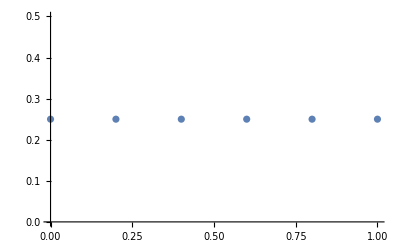

```mathematica
ListPlot[{{0,.2,.4,.6,.8,1},{0.24999999999999975,0.24999999999999947,0.24999999999999972,0.24999999999999944,0.24999999999999972,0.2500000000000001}}ᵀ]
```

```mathematica
ℱ[1]
```

{1.,{4.82292,4.04801,1.71256,5.48456,5.93148,1.04351,4.90619,4.54453,2.29651,0.0530933,0.212899,1.16773,5.49779,1.8817,4.15058}}

```mathematica
pr//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Partition[IdentityMatrix[4]⊙({{1, 0}, {0, 0}}),{4,4}]//MatrixForm
```

((1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0))

```mathematica
A=Array[Subscript[a, #1,#2]&,{4,4}]
B=Array[Subscript[b, #1,#2]&,{2,2}]
MatrixForm[Partition[#,{2,2}]]&/@{A⊙B,pr.A⊙B.pr,pt[pr.A⊙B.pr]}
```

{{a_(1,1),a_(1,2),a_(1,3),a_(1,4)},{a_(2,1),a_(2,2),a_(2,3),a_(2,4)},{a_(3,1),a_(3,2),a_(3,3),a_(3,4)},{a_(4,1),a_(4,2),a_(4,3),a_(4,4)}}

{{b_(1,1),b_(1,2)},{b_(2,1),b_(2,2)}}

{((a_(1,1) b_(1,1) | a_(1,1) b_(1,2)
a_(1,1) b_(2,1) | a_(1,1) b_(2,2)) | (a_(1,2) b_(1,1) | a_(1,2) b_(1,2)
a_(1,2) b_(2,1) | a_(1,2) b_(2,2)) | (a_(1,3) b_(1,1) | a_(1,3) b_(1,2)
a_(1,3) b_(2,1) | a_(1,3) b_(2,2)) | (a_(1,4) b_(1,1) | a_(1,4) b_(1,2)
a_(1,4) b_(2,1) | a_(1,4) b_(2,2))
(a_(2,1) b_(1,1) | a_(2,1) b_(1,2)
a_(2,1) b_(2,1) | a_(2,1) b_(2,2)) | (a_(2,2) b_(1,1) | a_(2,2) b_(1,2)
a_(2,2) b_(2,1) | a_(2,2) b_(2,2)) | (a_(2,3) b_(1,1) | a_(2,3) b_(1,2)
a_(2,3) b_(2,1) | a_(2,3) b_(2,2)) | (a_(2,4) b_(1,1) | a_(2,4) b_(1,2)
a_(2,4) b_(2,1) | a_(2,4) b_(2,2))
(a_(3,1) b_(1,1) | a_(3,1) b_(1,2)
a_(3,1) b_(2,1) | a_(3,1) b_(2,2)) | (a_(3,2) b_(1,1) | a_(3,2) b_(1,2)
a_(3,2) b_(2,1) | a_(3,2) b_(2,2)) | (a_(3,3) b_(1,1) | a_(3,3) b_(1,2)
a_(3,3) b_(2,1) | a_(3,3) b_(2,2)) | (a_(3,4) b_(1,1) | a_(3,4) b_(1,2)
a_(3,4) b_(2,1) | a_(3,4) b_(2,2))
(a_(4,1) b_(1,1) | a_(4,1) b_(1,2)
a_(4,1) b_(2,1) | a_(4,1) b_(2,2)) | (a_(4,2) b_(1,1) | a_(4,2) b_(1,2)
a_(4,2) b_(2,1) | a_(4,2) b_(2,2)) | (a_(4,3) b_(1,1) | a_(4,3) b_(1,2)
a_(4,3) b_(2,1) | a_(4,3) b_(2,2)) | (a_(4,4) b_(1,1) | a_(4,4) b_(1,2)
a_(4,4) b_(2,1) | a_(4,4) b_(2,2))),((a_(1,1) b_(1,1) | 0
0 | 0) | (a_(1,2) b_(1,1) | 0
0 | 0) | (a_(1,3) b_(1,1) | 0
0 | 0) | (a_(1,4) b_(1,1) | 0
0 | 0)
(a_(2,1) b_(1,1) | 0
0 | 0) | (a_(2,2) b_(1,1) | 0
0 | 0) | (a_(2,3) b_(1,1) | 0
0 | 0) | (a_(2,4) b_(1,1) | 0
0 | 0)
(a_(3,1) b_(1,1) | 0
0 | 0) | (a_(3,2) b_(1,1) | 0
0 | 0) | (a_(3,3) b_(1,1) | 0
0 | 0) | (a_(3,4) b_(1,1) | 0
0 | 0)
(a_(4,1) b_(1,1) | 0
0 | 0) | (a_(4,2) b_(1,1) | 0
0 | 0) | (a_(4,3) b_(1,1) | 0
0 | 0) | (a_(4,4) b_(1,1) | 0
0 | 0)),((a_(1,1) b_(1,1) | a_(1,2) b_(1,1)
a_(2,1) b_(1,1) | a_(2,2) b_(1,1)) | (a_(1,3) b_(1,1) | a_(1,4) b_(1,1)
a_(2,3) b_(1,1) | a_(2,4) b_(1,1))
(a_(3,1) b_(1,1) | a_(3,2) b_(1,1)
a_(4,1) b_(1,1) | a_(4,2) b_(1,1)) | (a_(3,3) b_(1,1) | a_(3,4) b_(1,1)
a_(4,3) b_(1,1) | a_(4,4) b_(1,1)))}

```mathematica
pt[pr.(Array[Subscript[m, #1,#2]&,{8,8}]).pr]//MatrixForm
```

(m_(1,1) | m_(1,3) | m_(1,5) | m_(1,7)
m_(3,1) | m_(3,3) | m_(3,5) | m_(3,7)
m_(5,1) | m_(5,3) | m_(5,5) | m_(5,7)
m_(7,1) | m_(7,3) | m_(7,5) | m_(7,7))